## 13 TeV with PDF Monolepton

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dCθ *)

dσhatdCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/alpha_scheme-udbar2lpv_X-sec.txt"]]/.x->1


(*ToParton={s->shat, t->that,u->uhat};*)
```

(80698.2 Ein^2 (4.39959×10^-9 (-61.5549 (δGF6^2-2 √2 δGF8)+174.104 δGF6+246.22)^4 (Cθ^2 (4 CHL36til^2+8 CHL36til (2 CHQ36til+1)+4 CHL38til+4 CHQ36til^2+8 CHQ36til+4 CHQ38til+CHud6til^2+4)-2 Cθ (4 CHL36til^2+8 CHL36til (2 CHQ36til+1)+4 CHL38til+4 CHQ36til^2+8 CHQ36til+4 CHQ38til-CHud6til^2+4)+4 CHL36til^2+8 CHL36til (2 CHQ36til+1)+4 CHL38til+4 CHQ36til^2+8 CHQ36til+4 CHQ38til+CHud6til^2+4) (-62.4713 CHB6til CHWB6til+0.53806 (-8 (3 CHD28til+3 CHD8til+24 CHW28til+10 CHWB6til^2-19 δGF6^2+12 √2 δGF6+12 √2 δGF8-48)+19 CHD6til^2+4 CHD6til (7 √2 δGF6-12))+6.73573 (CHD28til-CHD6til^2+CHD6til (2-2 √2 δGF6)+CHD8til-8 δGF6^2+4 √2 δGF6+4 √2 δGF8)-8.07129 CHD28til+3.04456 CHD6til^2-31.624 CHD6til CHWB6til-5.60644 CHD6til δGF6-16.1426 CHD6til-8.07129 CHD8til+63.4296 CHW28til-62.4713 CHW6til CHWB6til-80.4278 CHWB6til^2-89.4462 CHWB6til δGF6-62.4713 CHWB6til-946817. CHWB8til+24.3565 δGF6^2-64 √2 δGF6+44.8515 δGF6-64 √2 δGF8+44.8515 δGF8-126.859)^4+0.000132659 (Cθ-1)^2 (4 Ein^2-(-28.5733 CHD6til-62.6363 CHWB6til-24.2727 δGF6+79.9664)^2) (-62.4713 CHB6til CHWB6til+0.53806 (-8 (3 CHD28til+3 CHD8til+24 CHW28til+10 CHWB6til^2-19 δGF6^2+12 √2 δGF6+12 √2 δGF8-48)+19 CHD6til^2+4 CHD6til (7 √2 δGF6-12))+6.73573 (CHD28til-CHD6til^2+CHD6til (2-2 √2 δGF6)+CHD8til-8 δGF6^2+4 √2 δGF6+4 √2 δGF8)-8.07129 CHD28til+3.04456 CHD6til^2-31.624 CHD6til CHWB6til-5.60644 CHD6til δGF6-16.1426 CHD6til-8.07129 CHD8til+63.4296 CHW28til-62.4713 CHW6til CHWB6til-80.4278 CHWB6til^2-89.4462 CHWB6til δGF6-62.4713 CHWB6til-946817. CHWB8til+24.3565 δGF6^2-64 √2 δGF6+44.8515 δGF6-64 √2 δGF8+44.8515 δGF8-126.859)^2 (4 CLQ36til (CHL36til+CHQ36til+1) (-61.5549 (δGF6^2-2 √2 δGF8)+174.104 δGF6+246.22)^2+(2 CHLQ28til+CHLQ58til) (-61.5549 (δGF6^2-2 √2 δGF8)+174.104 δGF6+246.22)^2-8 CLQs38til Ein^2-4 (Cθ+1) CLQt38til Ein^2)+4 (Cθ-1)^2 CLQ36til^2 ((-28.5733 CHD6til-62.6363 CHWB6til-24.2727 δGF6+79.9664)^4-8 Ein^2 (-28.5733 CHD6til-62.6363 CHWB6til-24.2727 δGF6+79.9664)^2+16 Ein^4)))/((-61.5549 (δGF6^2-2 √2 δGF8)+174.104 δGF6+246.22)^4 ((-28.5733 CHD6til-62.6363 CHWB6til-24.2727 δGF6+79.9664)^4-8 Ein^2 (-28.5733 CHD6til-62.6363 CHWB6til-24.2727 δGF6+79.9664)^2+16 Ein^4))

### Assign Wilson Coefficients

```mathematica
wilsonCoeflist={};
onlySM={};
variablelist = DeleteDuplicates@Cases[dσhatdCθ,_Symbol,Infinity]
variablelist=Delete[variablelist,{{1},{7}}]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->5*10^-6]]
For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[onlySM,variablelist[[coef]]->0.]]


dσdCθwil = dσhatdCθ/.wilsonCoeflist
dσdCθSM = dσhatdCθ/.onlySM
```

{Ein,CHD6til,CHWB6til,δGF6,δGF8,CLQ36til,Cθ,CLQs38til,CLQt38til,CHLQ28til,CHLQ58til,CHL36til,CHQ36til,CHD28til,CHD8til,CHW28til,CHB6til,CHW6til,CHWB8til,CHL38til,CHQ38til,CHud6til}

{CHD6til,CHWB6til,δGF6,δGF8,CLQ36til,CLQs38til,CLQt38til,CHLQ28til,CHLQ58til,CHL36til,CHQ36til,CHD28til,CHD8til,CHW28til,CHB6til,CHW6til,CHWB8til,CHL38til,CHQ38til,CHud6til}

(0.0000219564 Ein^2 (5.12181×10^8 ((6400192001 Cθ^2)/1600000000-(160004800023 Cθ)/20000000000+6400192001/1600000000)+0.746604 (Cθ-1)^2 (4 Ein^2-6394.53) (-((Cθ+1) Ein^2)/50000-Ein^2/25000+2.12189)+((Cθ-1)^2 (16 Ein^4-51156.2 Ein^2+4.089×10^7))/10000000000))/(16 Ein^4-51156.2 Ein^2+4.089×10^7)

(0.000021957 (6.54259×10^8 (4. Cθ^2-8. Cθ+4.)+0.) Ein^2)/(16 Ein^4-51157. Ein^2+4.08912×10^7)

### PDF Convolution

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/PDF/MSTW2008code"
SetDirectory[pdfpath];
<< mstwpdf.m
prefix=pdfpath<>"/Grids/mstw2008nnlo";
Timing[ReadPDFGrid[prefix,0]]
```

~/Google Drive/Research/Instruction/Tools/PDF/MSTW2008code

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from ~/Google Drive/Research/Instruction/Tools/PDF/MSTW2008code/Grids/mstw2008nnlo.00.dat

{4.08402,Null}

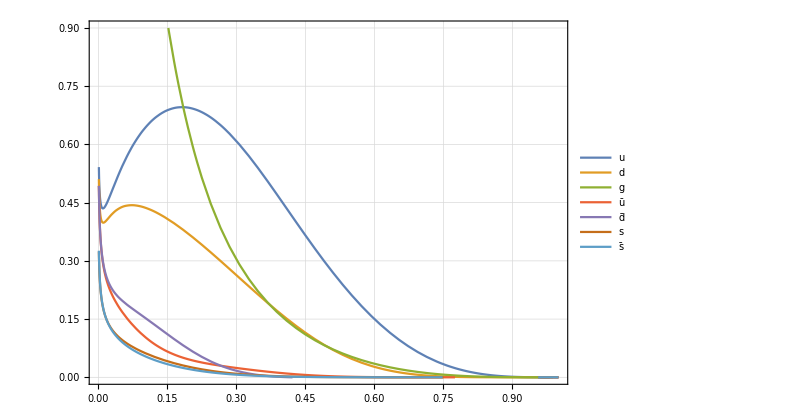

```mathematica
(* Plot PDF : Peskin pg 563 *)
uppdf=xf[0,x,2,2];
downpdf=xf[0,x,2,1];
gluepdf=xf[0,x,2,0];
upbarpdf=xf[0,x,2,-2];
dbarpdf=xf[0,x,2,-1];
spdf=xf[0,x,2,3];
sbarpdf=xf[0,x,2,-3];
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.001,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;

pdf[x_,Q_,flav_]:=If[x<1.0&&x>10^-7,1/x xf[0,x,Q,flav],0]

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

(* Parton Luminosity (Factorization) *)
Lq[list_,ecoll_,M1_,M2_,quarkID1_,quarkID2_]:=Block[{ArrayL1,Mcounts,Mvalue,IntL,Qgluon},
ArrayL1={};
Mcounts=71;
If[quarkID1==0 && quarkID2==0,Qgluon=-1,Qgluon=1];
Monitor[For[j=1,j≤Mcounts,j+=1,
Mvalue=(M1+(M2-M1)/(Mcounts-1)(j-1))//N;
AppendTo[ArrayL1,{Mvalue,(2Mvalue)/ecoll^2 NIntegrate[1/(x((1-Qgluon)/2+1))(pdf[x, Mvalue,quarkID1]pdf[Mvalue^2/(x ecoll^2), Mvalue,quarkID2]+pdf[x, Mvalue,quarkID2]pdf[Mvalue^2/(x ecoll^2), Mvalue,quarkID1]),{x,Mvalue^2/ecoll^2,1}]}];
(*((1-Qgluon)/2+1) for glue-glue collision*) (* 2Mvalue comes from d/dM^2 -> 1/(2M)d/dM*)

],j];
(* Interpolate *)
IntL=Interpolation[ArrayL1];
(* Output *)
If[list==1,Return[ArrayL1],Return[IntL]]
]

(* We now calculate the DATA for the Luminosity functions to be used later *)

LudbarList=     Lq[1,ecoll,200,2700,2,-1];
(*Export["~/Dropbox/1_Dilepton_study/Luminosity_up_list.txt",LupList];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00198438}. NIntegrate obtained 21076.1 and 0.0712366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00721646}. NIntegrate obtained 12704.6 and 0.107331 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00218329}. NIntegrate obtained 8166.94 and 0.0304848 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction[…]

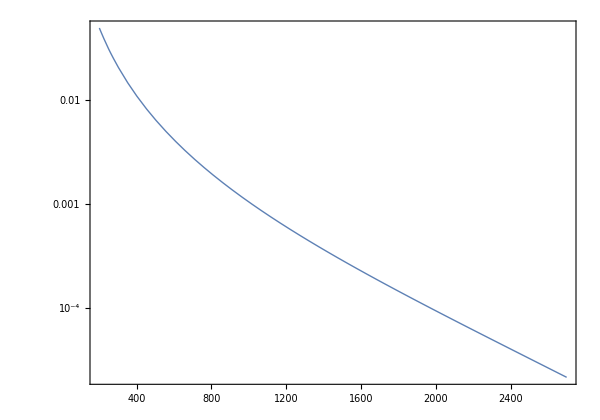

```mathematica
Ludbar=Interpolation[LudbarList]

LogPlot[Ludbar[x],{x,200,2700},Frame->True,PlotRange->All]
```

### Proton Level Calculation

#### dσ/dM Calculation

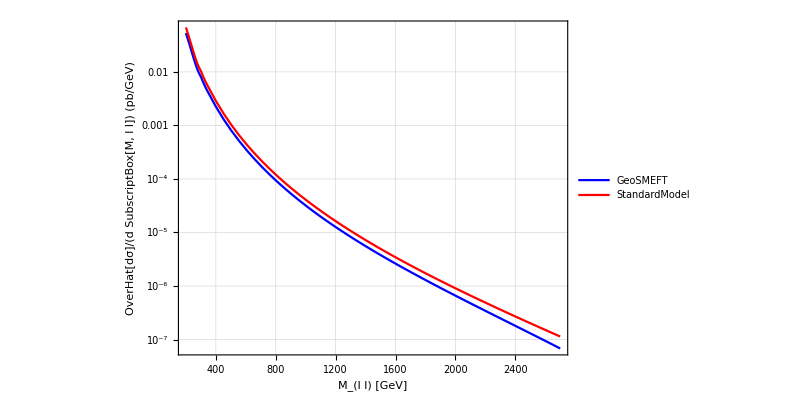

```mathematica
dσdCθdM[M_]:=Ludbar[M] (dσdCθwil/.{Ein->M/2})
dσdCθdMSM[M_]:=Ludbar[M] (dσdCθSM/.{Ein->M/2})


DataPoints=51;
InitialPoint=200;
FinalPoint=2700;
Step=(FinalPoint-InitialPoint)/(DataPoints-1)//N;

dσdM[M_]:=NIntegrate[dσdCθdM[M],{Cθ,-1,1}]
dσdMSM[M_]:=NIntegrate[dσdCθdMSM[M],{Cθ,-1,1}]

dσdMlist={};
dσdMSMlist={};

Monitor[For[j=1,j≤DataPoints,j+=1,

MVal=InitialPoint+Step(j-1);

AppendTo[dσdMlist,{MVal,dσdM[MVal]}];

AppendTo[dσdMSMlist,{MVal,dσdMSM[MVal]}];
],j];

dσdMIn=Interpolation[dσdMlist];
dσdMSMIn=Interpolation[dσdMSMlist];

dσdMplot=LogPlot[dσdMIn[M],{M,200,2700},PlotStyle->{Blue},PlotRange->All,FrameLabel->{"M_(l l) [GeV]",Style["OverHat[dσ]/(d SubscriptBox[M, l l]) (pb/GeV)"],"Mono-Lepton - proton Level"},PlotLegends->{"GeoSMEFT"}];
dσdMSMplot=LogPlot[dσdMSMIn[M],{M,200,2700},PlotStyle->{Red},PlotRange->All,FrameLabel->{"M_(l l) [GeV]",Style["OverHat[dσ]/(d SubscriptBox[M, l l]) (pb/GeV)"],"Mono-Lepton - proton Level"},PlotLegends->{"StandardModel"}];
Show[dσdMplot,dσdMSMplot]
```